# Ma3 - HW7

## Problem 1 - Calculations

```mathematica
data={{4,21},{5,25},{6,24},{7,39}};
expected={{4,16.45},{5,29.03},{6,32.85},{7,30.67}};
```

```mathematica
d=Sum[(data[[i]][[2]]-expected[[i]][[2]])^2/(expected[[i]][[2]]),{i,1,Length[data]}]
```

6.46465

```mathematica
crit=InverseCDF[ChiSquareDistribution[2],0.95]
```

5.99146

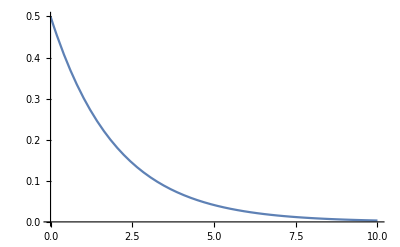

```mathematica
Plot[PDF[ChiSquareDistribution[2],x],{x,0,10}]
```

```mathematica
p=1-CDF[ChiSquareDistribution[2],d]
```

0.0394657

## Problem 2

Part (2)

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["SimplifiedEarthquakeCatalog2018.txt","Table"];
```

```mathematica
dates=data[[All,1]];
```

```mathematica
interArrivalTimes=Differences[dates];
```

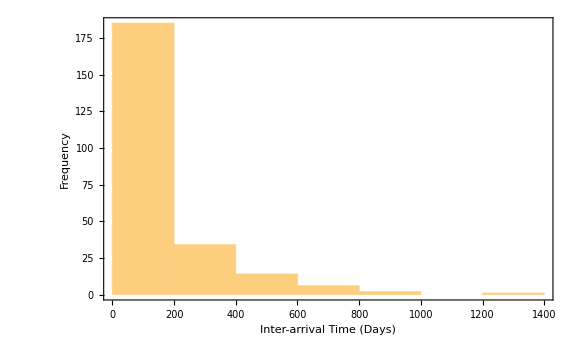

```mathematica
Histogram[interArrivalTimes,10,ImageSize->Large,Frame->True,FrameLabel->{"Inter-arrival Time (Days)","Frequency"}]
```

Part (3)

```mathematica
Mean[interArrivalTimes]
StandardDeviation[interArrivalTimes]
```

125.65

198.887

Part (6)

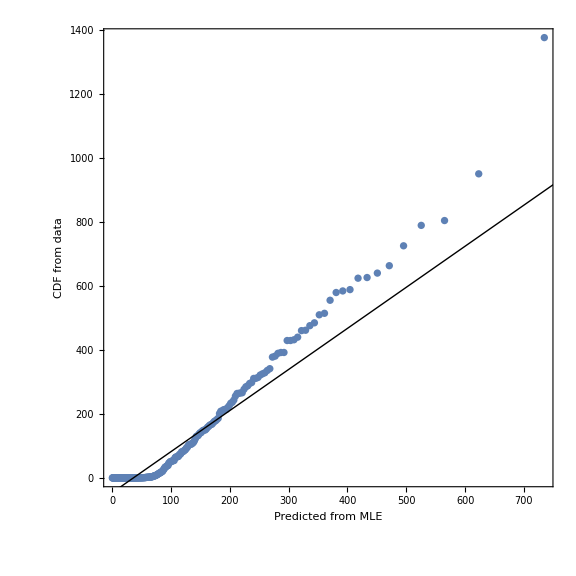

```mathematica
QuantilePlot[interArrivalTimes,ExponentialDistribution[1/Mean[interArrivalTimes]],AspectRatio->1,ImageSize->Large,FrameLabel->{"Predicted from MLE","CDF from data"},PlotRange->All]
```

Part (7)

```mathematica
KolmogorovSmirnovTest[interArrivalTimes,ExponentialDistribution[1/Mean[interArrivalTimes]]]//Quiet
```

2.90916×10^-33

Part (8)

```mathematica
restrictedInterArrivalTimes=Select[interArrivalTimes,#>4&];
```

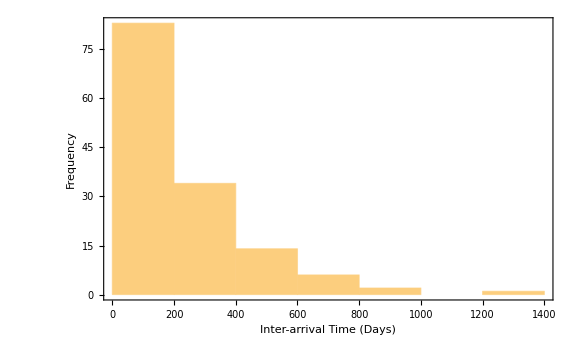

```mathematica
Histogram[restrictedInterArrivalTimes,10,ImageSize->Large,Frame->True,FrameLabel->{"Inter-arrival Time (Days)","Frequency"}]
```

```mathematica
Mean[restrictedInterArrivalTimes]
StandardDeviation[restrictedInterArrivalTimes]
```

216.863

220.684

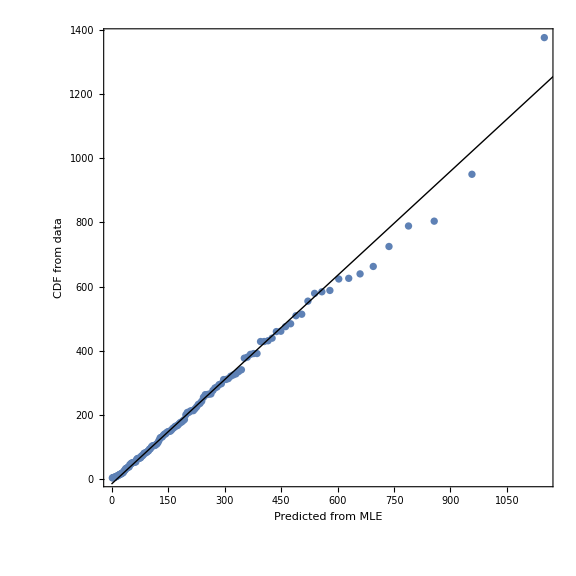

```mathematica
QuantilePlot[restrictedInterArrivalTimes,ExponentialDistribution[1/Mean[restrictedInterArrivalTimes]],AspectRatio->1,ImageSize->Large,FrameLabel->{"Predicted from MLE","CDF from data"},PlotRange->All]
```

```mathematica
KolmogorovSmirnovTest[restrictedInterArrivalTimes,ExponentialDistribution[1/Mean[restrictedInterArrivalTimes]]]
```

0.981649

Part (11)

```mathematica
includeIndices=Position[interArrivalTimes,_?(#>4&)];
```

```mathematica
includeList=Table[includeIndices[[i]][[1]],{i,1,Length[includeIndices]}];
```

```mathematica
restrictedData=dates[[includeList]];
```

```mathematica
yearData=Table[Floor[restrictedData[[i]]/365],{i,1,Length[restrictedData]}];
```

```mathematica
yearTally=Map[{#,Count[yearData,#]}&,Table[i,{i,1,Max[yearData]}]];
```

```mathematica
tallyList=Table[yearTally[[i]][[2]],{i,1,Length[yearTally]}];
```

```mathematica
distribution=Table[{i,Count[tallyList,i]},{i,0,8}];
```

```mathematica
distributionTable=Join[{{"# of Earthquakes","# of Years"}},distribution]//Transpose;
```

```mathematica
Grid[distributionTable,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},None}]
```

# of Earthquakes | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
# of Years | 15 | 25 | 23 | 11 | 4 | 1 | 1 | 0 | 1

```mathematica
n=Sum[distribution[[i]][[1]]*distribution[[i]][[2]],{i,1,Length[distribution]}]
```

139

```mathematica
μ=Mean[tallyList]//N
```

1.71605

```mathematica
var=Variance[tallyList]//N
```

2.08086

```mathematica
expectedEarthquakes=Table[{i,n*PDF[PoissonDistribution[μ],i]},{i,0,8}];
```

```mathematica
modExpected=Append[Table[expectedEarthquakes[[i]],{i,1,4}],{"≥ 4",Sum[expectedEarthquakes[[i]][[2]],{i,5,9}]}];
```

```mathematica
modData=Append[Table[distribution[[i]],{i,1,4}],{"≥ 4",Sum[distribution[[i]][[2]],{i,5,9}]}];
```

```mathematica
completeSet=Table[{modExpected[[i]][[1]],modExpected[[i]][[2]],modData[[i]][[2]]},{i,1,Length[modData]}];
```

```mathematica
completeTable=Join[{{"# of Earthquakes","Expected # of Years","Observed # of Years"}},completeSet]//Transpose;
```

```mathematica
Grid[completeTable,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},None}]
```

# of Earthquakes | 0 | 1 | 2 | 3 | ≥ 4
Expected # of Years | 24.9887 | 42.8819 | 36.7937 | 21.0466 | 13.2784
Observed # of Years | 15 | 25 | 23 | 11 | 7

```mathematica
d=Sum[(completeSet[[i]][[2]]-completeSet[[i]][[3]])^2/(completeSet[[i]][[2]]),{i,1,5}]
```

24.3851

```mathematica
InverseCDF[ChiSquareDistribution[3],0.95]
```

7.81473